{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

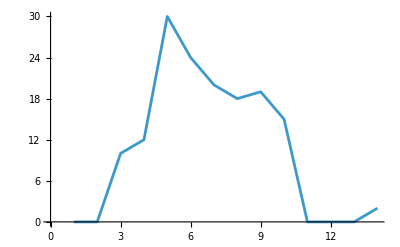

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
cwt=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

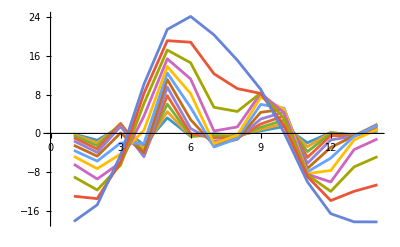

```mathematica
ListLinePlot[cwt[All,"Values"]]
```

```mathematica
cwt[All,"Values"]//Dimensions
```

{12,14}

{0,0,10,12,30,40,60,100,110,111}

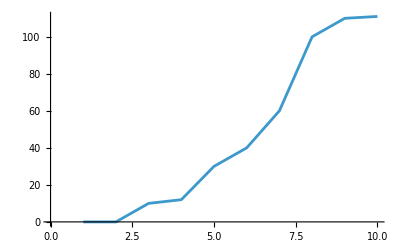

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

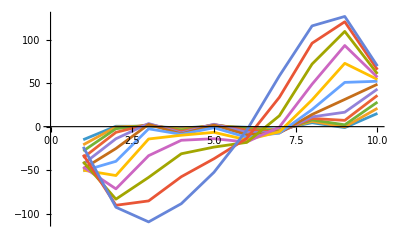

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.866826,0.713496,0.105614,0.14352,0.128965,0.943065,0.0971398,0.590297,0.194136,0.741395}

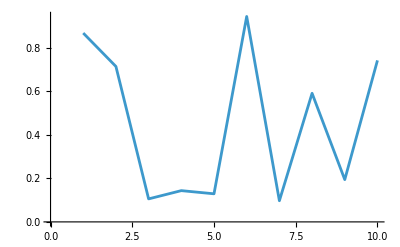

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

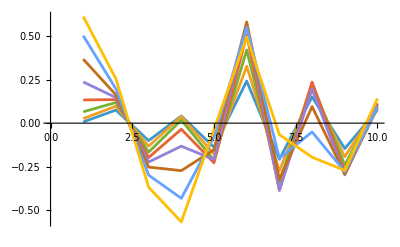

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```